```mathematica
SetOptions[Plot,Frame->True,PlotStyle->Dashing[{.05,.01}]];
```

```mathematica
f[x_]:=1/π^0.25 Exp[-1/2 x^2]
```

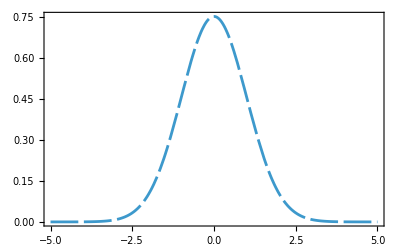

```mathematica
f1 = Plot[1/π^0.25 Exp[-1/2 x^2],{x,-5,5}, Frame->True]
```

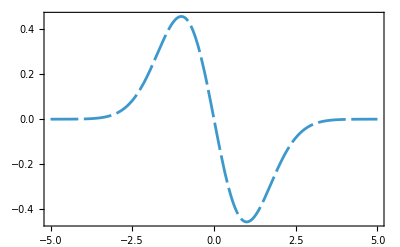

```mathematica
firtsD = Plot[Evaluate[D[f[x],x]],{x,-5,5}, Frame->True]
```

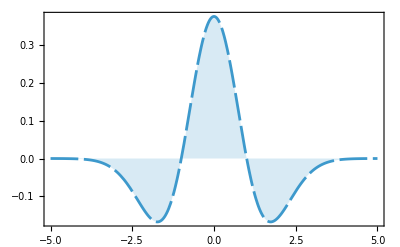

```mathematica
secondD = Plot[Evaluate[-0.5*D[D[f[x],x],x]],{x,-5,5}, Filling->Axis]
```

```mathematica
NIntegrate[-0.5D[f[x],{x,2}],{x,-5,5}]
```

0.0000139959

```mathematica
-0.5
```

```mathematica
NIntegrate[D[f[x],{x,2}],{x,-5,5}]
```

-0.0000279918

```mathematica
-0.5*NIntegrate[0.751126 ⅇ^(-x^2/2)+0.751126 ⅇ^(-x^2/2) x^2,{x,-5,5}]
```

-1.88278

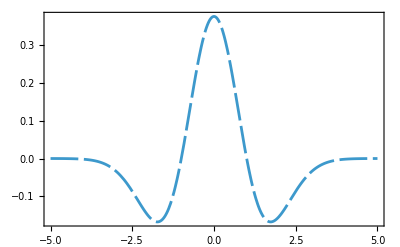
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{f1, firtsD, secondD}
```